# Deriving the empirical correlation function and fitting a curve to it

## Translating from “Towards a unified descriptive theory for spatial ecology” (who only provide a PDF of their Mathematica notebook!)

M Scott & M Osmond
2016 January 21

## Method with random data

Define the spatial extent of the area of interest (e.g., Barro Colorado Island)

```mathematica
{Lx,Ly}={1000,500}; (*total x and y distance of area of interest, ie a grid with length Lx and width Ly*)
Asub=100;(*space between coordinates, ie we chop up the total area into squares with length Asub; best if this divides the total space nicely, ie Lx/Asub and Ly/Asub are integers*)
```

Make up the data (because the authors suck at making it available)

```mathematica
numplots=10000;(*number of plots/datapoints*)
data=Table[{{RandomVariate[UniformDistribution[{0,Lx}]],RandomVariate[UniformDistribution[{0,Ly}]]},RandomInteger[{1,3}],RandomInteger[10]},{i,1,numplots}];
(*(x,y) locations of each plot, species code of each plot,abundance of that species in each plot*)
```

Get each variable of interest from data table

```mathematica
gx=Table[Transpose[data][[1]][[i,1]],{i,1,numplots}]; (*x coordinates of all plots*)
gy=Table[Transpose[data][[1]][[i,2]],{i,1,numplots}]; (*y coordinates of all plots*)
sp=Transpose[data][[2]];(*species code for each plot*)
ab=Transpose[data][[3]];(*species abundance at each plot*)
```

Some summary statistics of the data

```mathematica
Uspecie=Union[sp];(*vector of species IDs*)
Nspecies=Length[Uspecie];(*total number of species*)
TotAbundance=Total[ab];(*total abundance, across all species*)
```

Defining the coordinate system of the area

```mathematica
allpos=Tuples[{Range[Lx/Asub],Range[Ly/Asub]}]; (*coordinates, in translated form, ie. {1,1}, {1,2}, ..., {2,1}, {2,2}, ..., {m,n}*)
xyCpos=Flatten[Table[{(2 i+1)/2,(2 j+1)/2}// N,{i,0,(Lx/Asub)-1,1},{j,0,(Ly/Asub)-1,1}],1];(*halfway points between coordinates, which we use later to derive the distances between centers of each "bin" (area below (south) and to left (west) of each coordinate*)
allpair=Tuples[{allpos,allpos}];(*pairs of each translated coordinate with each other, e.g., {{1,1},{1,1}}*)
nplot=Range[Length[allpos]]; (*total number of coordinates/bins*)
```

Locations of plots (the bin they are in)

```mathematica
Xpos[p_]:=Flatten[Position[gx,x_?(Asub*(p-1) ≤ #<Asub*p&)],1](*which plots (their position in the data vector) have x location between two coordinates, for all pairs of x coordinates; for p between 1 and Lx/Asub*)
Ypos[q_]:=Flatten[Position[gy,x_?(Asub*(q-1) ≤ #<Asub*q&)],1](*which plots have y location between two coordinates, for all pairs of y coordinates; for q between 1 and Ly/Asub*)
rule1=Flatten[Table[{allpos[[i]] -> nplot[[i]]},{i,1,Length[allpos]}],1];(*translate from coordinates (tuple) to single identifying number*)
rule2=Flatten[Table[{nplot[[i]] -> allpos[[i]]},{i,1,Length[allpos]}],1];(*translate back*)
XYpos[{p_,q_}]:=Intersection[Xpos[p],Ypos[q]];(*which plots have location (x,y) within (x(p-1),x p) and (y(p-1), y p)*)
possub=ParallelMap[XYpos,allpos];(*which plots fall in which bin (e.g., (x,y)=(321,434), with Asub=100, would fall in (400,500)*)
```

Which species are where

```mathematica
XYS[i_]:=Transpose[{gx[[possub[[i]]]],gy[[possub[[i]]]],sp[[possub[[i]]]]}];(*gives (x,y) location of plots, and sp code, in each bin*)
SabA[i_]:=Count[sp[[possub[[i]]]],#]&/@ Uspecie (*number of plots with each species in each bin*)
SA[i_]:=Boole/@ (MemberQ[sp[[possub[[i]]]],#]&/@ Uspecie) (*1 if at least one plot with a species in given bin, ie presence/absence in bin*)
Spos=Table[SA[i],{i,1,Length[possub]}];(*table with all bins*)
```

Covariance in species abundance by distances

```mathematica
dist[{i_,j_}]:=Sqrt[Total[(Abs[xyCpos[[i]]-xyCpos[[j]]])^2]] (*Euclidean distance between center of two bins (in translated space; need to multiply by Asub to get real distances, which we do later)*)
index[{i_,j_}]:={i,j}(*not sure what this does, but doesnt hurt*)
alldist=Map[dist,allpair/.rule1]; (*distance between center of all pairs of bins*)
rvec=Union[alldist];(*all unique distances in increasing order*)
indexpair=Map[index,allpair/. rule1];(*translate from tuples of coordinates to pairs of coordinate indices*)
posdist=Position[alldist,#]&/@ rvec;(*identify coordinate index pairs whose bin centers are given distance apart*)
Cov[{i_,j_}]:=Mean[SabA[i] SabA[j]]/(Mean[SabA[i]] Mean[SabA[j]])//N;(*"covariance" in number of plots with species across bins, note that the "covariance" is taken over all species, ie "covariance" in community composition*)
allcov=ParallelTable[Map[Cov,indexpair[[Flatten[posdist[[i]],1]]]],{i,1,Length[rvec]}];(*covaraiance in number of plots with species at each distance*)
```

Our empirical correlation function

```mathematica
empPCF=Transpose[{rvec*Asub,Map[Mean,allcov]}];(*empirical correlation function, PCF; first element of each pair is the (untranslated) distance between the center of two bins (rvec*Asub), the second element is the mean covariance in number of plots with species across all pairs of bins that distance apart*)
```

which looks like this

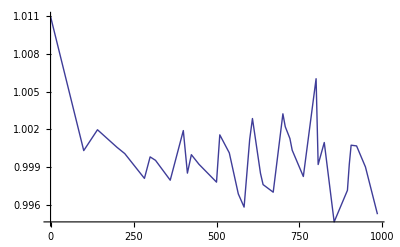

```mathematica
ListPlot[empPCF,Joined->True]
```

Fitting the function to the data

```mathematica
g[r_]:=1+1/(2π)(ρ/λ)^2 BesselK[0,r/λ](*function to fit to the empirical PCF*)
λ=.;(*what does this do?*)
ρ=.;
fitcor=NonlinearModelFit[Rest[empPCF],g[r],{{λ,10^9},{ρ,0.1}},r];(*fit the function, with some parameter guesses*)
```

How good is the fit?

```mathematica
Grid[Transpose[{#,fitcor[#]}&[{"AdjustedRSquared","AIC","BIC","RSquared"}]],Alignment -> Left](*stats for fit*)
```

AdjustedRSquared | 0.999994
AIC | -338.091
BIC | -333.258
RSquared | 0.999995

What are our parameter estimates?

```mathematica
fitcor["ParameterTable"](*stats for parameter estimates*)
σλ1=fitcor["ParameterTableEntries"][[1,2]];(*standard error for lambda*)
σρ1=fitcor["ParameterTableEntries"][[2,2]];(*standard error for rho*)(*standard error for rho*)
```

| Estimate | Standard Error | t-Statistic | P-Value
λ | 1.×10^9 | 6.6103×10^27 | 1.51279×10^-19 | 1
ρ | 0.1 | 6.38383×10^17 | 1.56646×10^-19 | 1

Or if you like confidence intervals better...

```mathematica
fitcor["ParameterConfidenceIntervalTable"](*get confidence intervals too*)
```

| Estimate | Standard Error | Confidence Interval
λ | 1.×10^9 | 6.6103×10^27 | {-1.34196×10^28,1.34196×10^28}
ρ | 0.1 | 6.38383×10^17 | {-1.29599×10^18,1.29599×10^18}

Plot fitted curve with data points

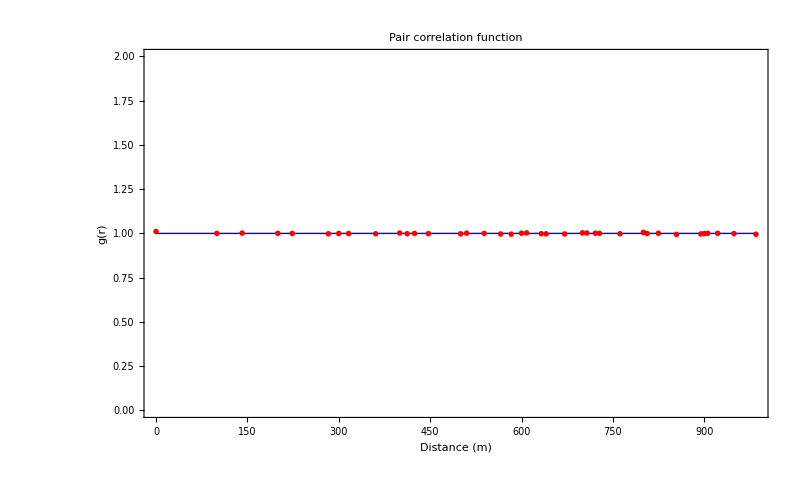

```mathematica
Plot[
fitcor[r],
{r,Min[rvec*Asub],Max[rvec*Asub]},
PlotStyle->{ Blue,Thick},
PlotRange->{{0,Max[rvec*Asub]},Automatic},
Frame ->{{True,False},{True,False}},
FrameLabel -> {"Distance (m)","g(r)"},
PlotLabel -> "Pair correlation function",
LabelStyle -> {FontFamily -> "Times",FontSize -> 12},
Prolog -> {Red,PointSize[0.005],Point/@ empPCF},
Axes->False,
ImageSize->800
]
```

Plot fitted curve with confidence bands

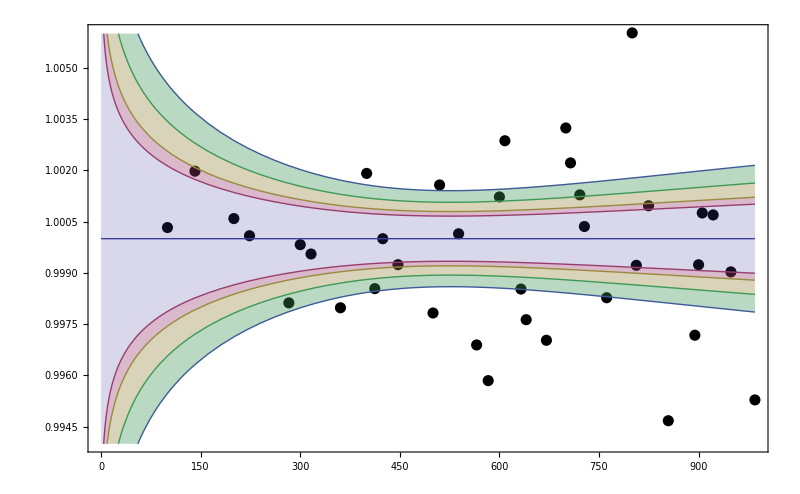

```mathematica
{bands90[x_],bands95[x_],bands99[x_],bands999[x_]} =Table[fitcor["MeanPredictionBands",ConfidenceLevel -> cl],{cl,{.9,.95,.99,.999}}];(*confidence bands*)
Show[
ListPlot[Rest[empPCF],PlotStyle->{Black,PointSize[0.01]},Axes->False],Plot[{fitcor[r],bands90[r],bands95[r],bands99[r],bands999[r]},{r,Min[rvec*Asub],Max[rvec*Asub]},Filling-> {2 ->{1},3 ->{2},4 ->{3},5 ->{4}}],
PlotRange->{{0,Max[rvec*Asub]},Automatic},
Frame->{True,True,False,False},
ImageSize->800]
```

## Simulated Data

Load data from Patrick’s simulation

```mathematica
datadir="/Users/mmosmond/Documents/PHD/MARYSCONVERT/";
simdata=Import[datadir<>"SimulatedAbundances"<>".csv"];
```

The data comes with 5 columns

```mathematica
simdata[[1]]
```

{x,y,Species,Abundance,Stress_abund}

x is the x location (1:20) y is the y location (1:20), species is species ID (1:80), abundance is number of individuals of that species in plot, and stress abundance is abundance under some stressor (we will eventually want to compare model results with and without stressor).

We first drop the column names

```mathematica
simdata=Drop[simdata,{1}];
```

Define the spatial extent of the area of interest

```mathematica
{Lx,Ly}={20,20}; (*total x and y distance of area of interest, ie a grid with length Lx and width Ly*)
Asub=2;(*space between coordinates, ie we chop up the total area into squares with length Asub; best if this divides the total space nicely, ie Lx/Asub and Ly/Asub are integers*)
```

Get each variable of interest from data table

```mathematica
gx=Transpose[simdata][[1]];
gy=Transpose[simdata][[2]];
sp=Transpose[simdata][[3]];
ab=Transpose[simdata][[4]];
stab=Transpose[simdata][[5]];
```

Some summary statistics of the data

```mathematica
Uspecie=Union[sp];(*vector of species IDs*)
Nspecies=Length[Uspecie];(*total number of species*)
TotAbundance=Total[ab];(*total abundance, across all species*)
```

Defining the coordinate system of the area

```mathematica
allpos=Tuples[{Range[Lx/Asub],Range[Ly/Asub]}]; (*coordinates, in translated form, ie. {1,1}, {1,2}, ..., {2,1}, {2,2}, ..., {m,n}*)
xyCpos=Flatten[Table[{(2 i+1)/2,(2 j+1)/2}// N,{i,0,(Lx/Asub)-1,1},{j,0,(Ly/Asub)-1,1}],1];(*halfway points between coordinates, which we use later to derive the distances between centers of each "bin" (area below (south) and to left (west) of each coordinate*)
allpair=Tuples[{allpos,allpos}];(*pairs of each translated coordinate with each other, e.g., {{1,1},{1,1}}*)
nplot=Range[Length[allpos]]; (*total number of coordinates/bins*)
```

Locations of plots (the bin they are in)

```mathematica
Xpos[p_]:=Flatten[Position[gx,x_?(Asub*(p-1) ≤ #<Asub*p&)],1](*which plots (their position in the data vector) have x location between two coordinates, for all pairs of x coordinates; for p between 1 and Lx/Asub*)
Ypos[q_]:=Flatten[Position[gy,x_?(Asub*(q-1) ≤ #<Asub*q&)],1](*which plots have y location between two coordinates, for all pairs of y coordinates; for q between 1 and Ly/Asub*)
rule1=Flatten[Table[{allpos[[i]] -> nplot[[i]]},{i,1,Length[allpos]}],1];(*translate from coordinates (tuple) to single identifying number*)
rule2=Flatten[Table[{nplot[[i]] -> allpos[[i]]},{i,1,Length[allpos]}],1];(*translate back*)
XYpos[{p_,q_}]:=Intersection[Xpos[p],Ypos[q]];(*which plots have location (x,y) within (x(p-1),x p) and (y(p-1), y p)*)
possub=ParallelMap[XYpos,allpos];(*which plots fall in which bin (e.g., (x,y)=(321,434), with Asub=100, would fall in (400,500)*)
```

Which species are where

```mathematica
possub[[1]]
```

{1,401,801,1201,1601,2001,2401,2801,3201,3601,4001,4401,4801,5201,5601,6001,6401,6801,7201,7601,8001,8401,8801,9201,9601,10001,10401,10801,11201,11601,12001,12401,12801,13201,13601,14001,14401,14801,15201,15601,16001,16401,16801,17201,17601,18001,18401,18801,19201,19601,20001,20401,20801,21201,21601,22001,22401,22801,23201,23601,24001,24401,24801,25201,25601,26001,26401,26801,27201,27601,28001,28401,28801,29201,29601,30001,30401,30801,31201,31601}

```mathematica
sp[[possub[[1]]]]
```

{Sp. 1,Sp. 2,Sp. 3,Sp. 4,Sp. 5,Sp. 6,Sp. 7,Sp. 8,Sp. 9,Sp. 10,Sp. 11,Sp. 12,Sp. 13,Sp. 14,Sp. 15,Sp. 16,Sp. 17,Sp. 18,Sp. 19,Sp. 20,Sp. 21,Sp. 22,Sp. 23,Sp. 24,Sp. 25,Sp. 26,Sp. 27,Sp. 28,Sp. 29,Sp. 30,Sp. 31,Sp. 32,Sp. 33,Sp. 34,Sp. 35,Sp. 36,Sp. 37,Sp. 38,Sp. 39,Sp. 40,Sp. 41,Sp. 42,Sp. 43,Sp. 44,Sp. 45,Sp. 46,Sp. 47,Sp. 48,Sp. 49,Sp. 50,Sp. 51,Sp. 52,Sp. 53,Sp. 54,Sp. 55,Sp. 56,Sp. 57,Sp. 58,Sp. 59,Sp. 60,Sp. 61,Sp. 62,Sp. 63,Sp. 64,Sp. 65,Sp. 66,Sp. 67,Sp. 68,Sp. 69,Sp. 70,Sp. 71,Sp. 72,Sp. 73,Sp. 74,Sp. 75,Sp. 76,Sp. 77,Sp. 78,Sp. 79,Sp. 80}

```mathematica
ab[[possub[[1]]]]
```

{0,0,0,0,0,0,0,0,0,451,0,0,0,0,4,0,0,0,0,14,0,1015,16,1330,34,0,12,0,0,678,0,247,24,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
simdata[[1]]
```

{1,1,Sp. 1,0,0}

```mathematica
(Count[sp[[possub[[1]]]],#]&/@ Uspecie)*ab[[possub[[1]]]]
```

{0,0,0,0,0,0,0,0,0,451,0,0,0,0,4,0,0,0,0,14,0,1015,16,1330,34,0,12,0,0,678,0,247,24,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
XYS[i_]:=Transpose[{gx[[possub[[i]]]],gy[[possub[[i]]]],sp[[possub[[i]]]]}];(*gives (x,y) location of plots, and sp code, in each bin*)
(*SabA[i_]:=Count[sp[[possub[[i]]]],#]&/@ Uspecie*) (*number of plots with each species in each bin*)
SabA[i_]:=(Count[sp[[possub[[i]]]],#]&/@ Uspecie)*ab[[possub[[i]]]]
SA[i_]:=Boole/@ (MemberQ[sp[[possub[[i]]]],#]&/@ Uspecie) (*1 if at least one plot with a species in given bin, ie presence/absence in bin*)
Spos=Table[SA[i],{i,1,Length[possub]}];(*table with all bins*)
```

Covariance in species abundance by distances

```mathematica
dist[{i_,j_}]:=Sqrt[Total[(Abs[xyCpos[[i]]-xyCpos[[j]]])^2]] (*Euclidean distance between center of two bins (in translated space; need to multiply by Asub to get real distances, which we do later)*)
index[{i_,j_}]:={i,j}(*not sure what this does, but doesnt hurt*)
alldist=Map[dist,allpair/.rule1]; (*distance between center of all pairs of bins*)
rvec=Union[alldist];(*all unique distances in increasing order*)
indexpair=Map[index,allpair/. rule1];(*translate from tuples of coordinates to pairs of coordinate indices*)
posdist=Position[alldist,#]&/@ rvec;(*identify coordinate index pairs whose bin centers are given distance apart*)
Cov[{i_,j_}]:=Mean[SabA[i] SabA[j]]-(Mean[SabA[i]] Mean[SabA[j]])//N;(*"covariance" in number of plots with species across bins, note that the "covariance" is taken over all species, ie "covariance" in community composition*)
allcov=ParallelTable[Map[Cov,indexpair[[Flatten[posdist[[i]],1]]]],{i,1,Length[rvec]}];(*covaraiance in number of plots with species at each distance*)
```

Thread::tdlen: Objects of unequal length in {2, 2, 2, 2, 2, 2, 2, 2, 2, 2, 2, 2, 2, 2, 2, 2, 2, 2, 2, 2, 2, 2, 2, 2, 2, 2, 2, 2, 2, 2, 2, 2, 2, 2, 2, 2, 2, 2, 2, 2, 2, 2, 2, 2, 2, 2, 2, 2, 2, 2, « 30 »}\ {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 16, 7, 0, 0, 1103, 1040, 11, 8, 1230, 1179, 252, 339, « 110 »} cannot be combined.

Thread::tdlen: Objects of unequal length in {4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, « 30 »}\ {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 4, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, « 270 »} cannot be combined.

Thread::tdlen: Objects of unequal length in {4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, « 30 »}\ {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, « 270 »} cannot be combined.

Thread::tdlen: Objects of unequal length in {2, 2, 2, 2, 2, 2, 2, 2, 2, 2, 2, 2, 2, 2, 2, 2, 2, 2, 2, 2, 2, 2, 2, 2, 2, 2, 2, 2, 2, 2, 2, 2, 2, 2, 2, 2, 2, 2, 2, 2, 2, 2, 2, 2, 2, 2, 2, 2, 2, 2, « 30 »}\ {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 16, 7, 0, 0, 1103, 1040, 11, 8, 1230, 1179, 252, 339, « 110 »} cannot be combined.

Thread::tdlen: Objects of unequal length in {0, 0, 0, 0, 0, 0, 0, 0, 0, 451, 0, 0, 0, 0, 4, 0, 0, 0, 0, 14, 0, 1015, 16, 1330, 34, 0, 12, 0, 0, 678, 0, 247, 24, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, « 30 »}\ {4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, « 30 »}\ {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 4, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, « 270 »} cannot be combined.

Thread::tdlen: Objects of unequal length in {0, 0, 0, 0, 0, 0, 0, 0, 0, 451, 0, 0, 0, 0, 4, 0, 0, 0, 0, 14, 0, 1015, 16, 1330, 34, 0, 12, 0, 0, 678, 0, 247, 24, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, « 30 »}\ {4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, « 30 »}\ {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, « 270 »} cannot be combined.

Thread::tdlen: Objects of unequal length in {2, 2, 2, 2, 2, 2, 2, 2, 2, 2, 2, 2, 2, 2, 2, 2, 2, 2, 2, 2, 2, 2, 2, 2, 2, 2, 2, 2, 2, 2, 2, 2, 2, 2, 2, 2, 2, 2, 2, 2, 2, 2, 2, 2, 2, 2, 2, 2, 2, 2, « 30 »}\ {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 16, 7, 0, 0, 1103, 1040, 11, 8, 1230, 1179, 252, 339, « 110 »}\ {2, 2, 2, 2, 2, 2, 2, 2, 2, 2, 2, 2, 2, 2, 2, 2, 2, 2, 2, 2, 2, 2, 2, 2, 2, 2, 2, 2, 2, 2, 2, 2, 2, 2, 2, 2, 2, 2, 2, 2, 2, 2, 2, 2, 2, 2, 2, 2, 2, 2, « 30 »}\ {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 16, 7, 0, 0, 1103, 1040, 11, 8, 1230, 1179, 252, 339, « 110 »} cannot be combined.

Thread::tdlen: Objects of unequal length in {4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, « 30 »}\ {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 4, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, « 270 »} cannot be combined.

Thread::tdlen: Objects of unequal length in {4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, « 30 »}\ {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, « 270 »} cannot be combined.

General::stop: Further output of Thread :: tdlen will be suppressed during this calculation.

Thread::tdlen: Objects of unequal length in {4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, « 30 »}\ {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, « 270 »} cannot be combined.

Thread::tdlen: Objects of unequal length in {0, 0, 0, 0, 0, 0, 0, 0, 0, 451, 0, 0, 0, 0, 4, 0, 0, 0, 0, 14, 0, 1015, 16, 1330, 34, 0, 12, 0, 0, 678, 0, 247, 24, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, « 30 »}\ {4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, « 30 »}\ {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, « 270 »} cannot be combined.

Thread::tdlen: Objects of unequal length in {4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, 4, « 30 »}\ {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, « 270 »} cannot be combined.

General::stop: Further output of Thread :: tdlen will be suppressed during this calculation.

$Aborted

Our empirical correlation function

```mathematica
empPCF=Transpose[{rvec*Asub,Map[Mean,allcov]}];(*empirical correlation function, PCF; first element of each pair is the (untranslated) distance between the center of two bins (rvec*Asub), the second element is the mean covariance in number of plots with species across all pairs of bins that distance apart*)
```

which looks like this

```mathematica
ListPlot[empPCF,Joined->True]
```

-Graphics-

Fitting the function to the data

```mathematica
g[r_]:=1+1/(2π)(ρ/λ)^2 BesselK[0,r/λ](*function to fit to the empirical PCF*)
λ=.;(*what does this do?*)
ρ=.;
fitcor=NonlinearModelFit[Rest[empPCF],g[r],{{λ,10^9},{ρ,0.1}},r];(*fit the function, with some parameter guesses*)
```

How good is the fit?

```mathematica
Grid[Transpose[{#,fitcor[#]}&[{"AdjustedRSquared","AIC","BIC","RSquared"}]],Alignment -> Left](*stats for fit*)
```

AdjustedRSquared | 0.999994
AIC | -338.091
BIC | -333.258
RSquared | 0.999995

What are our parameter estimates?

```mathematica
fitcor["ParameterTable"](*stats for parameter estimates*)
σλ1=fitcor["ParameterTableEntries"][[1,2]];(*standard error for lambda*)
σρ1=fitcor["ParameterTableEntries"][[2,2]];(*standard error for rho*)(*standard error for rho*)
```

| Estimate | Standard Error | t-Statistic | P-Value
λ | 1.×10^9 | 6.6103×10^27 | 1.51279×10^-19 | 1
ρ | 0.1 | 6.38383×10^17 | 1.56646×10^-19 | 1

Or if you like confidence intervals better...

```mathematica
fitcor["ParameterConfidenceIntervalTable"](*get confidence intervals too*)
```

| Estimate | Standard Error | Confidence Interval
λ | 1.×10^9 | 6.6103×10^27 | {-1.34196×10^28,1.34196×10^28}
ρ | 0.1 | 6.38383×10^17 | {-1.29599×10^18,1.29599×10^18}

Plot fitted curve with data points

```mathematica
Plot[
fitcor[r],
{r,Min[rvec*Asub],Max[rvec*Asub]},
PlotStyle->{ Blue,Thick},
PlotRange->{{0,Max[rvec*Asub]},Automatic},
Frame ->{{True,False},{True,False}},
FrameLabel -> {"Distance (m)","g(r)"},
PlotLabel -> "Pair correlation function",
LabelStyle -> {FontFamily -> "Times",FontSize -> 12},
Prolog -> {Red,PointSize[0.005],Point/@ empPCF},
Axes->False,
ImageSize->800
]
```

-Graphics-

Plot fitted curve with confidence bands

```mathematica
{bands90[x_],bands95[x_],bands99[x_],bands999[x_]} =Table[fitcor["MeanPredictionBands",ConfidenceLevel -> cl],{cl,{.9,.95,.99,.999}}];(*confidence bands*)
Show[
ListPlot[Rest[empPCF],PlotStyle->{Black,PointSize[0.01]},Axes->False],Plot[{fitcor[r],bands90[r],bands95[r],bands99[r],bands999[r]},{r,Min[rvec*Asub],Max[rvec*Asub]},Filling-> {2 ->{1},3 ->{2},4 ->{3},5 ->{4}}],
PlotRange->{{0,Max[rvec*Asub]},Automatic},
Frame->{True,True,False,False},
ImageSize->800]
```

-Graphics-